# checks

```mathematica
SetDirectory["/home/riccardorao/projects/fisheria/analysis"];
```

```mathematica
W = Import["Wmat.dat"];
```

```mathematica
W//MatrixForm
```

```mathematica
Q={
{1,Exp[Subscript[q, 5]],Exp[Subscript[q, 7]],1,Exp[Subscript[q, 11]]},
{Exp[Subscript[q, 1]],1,1,Exp[Subscript[q, 8]],Exp[Subscript[q, 12]]},
{Exp[Subscript[q, 3]],1,1,Exp[Subscript[q, 6]],1},
{1,Exp[Subscript[q, 4]],Exp[Subscript[q, 2]],1,1},
{1,1,Exp[Subscript[q, 9]],Exp[Subscript[q, 10]],1}
};
```

```mathematica
W*Q//MatrixForm
```

```mathematica
Λ=Det[ W*Q-Subscript[q, 13] IdentityMatrix[5]]
```

```mathematica
q0=Table[Subscript[q, i]->0,{i,13}];
```

```mathematica
Table[D[D[Λ, Subscript[q, j]], Subscript[q, i]],{i,1,13},{j,1,13}]/.q0//MatrixForm
```

```mathematica
jcov=Import["testJcov"];
```

```mathematica
Chop[jcov-Table[D[D[Λ, Subscript[q, j]], Subscript[q, i]],{i,1,13},{j,1,13}]/.q0,10^-11]
```

```mathematica
ave=Table[-D[Λ, Subscript[q, i]]/D[Λ, Subscript[q, 13]],{i,12}]/.q0
```

```mathematica
cov=Table[-(D[D[Λ, Subscript[q, j]], Subscript[q, i]]+ave⟦j⟧ D[D[Λ, Subscript[q, 13]], Subscript[q, i]]+ave⟦i⟧ D[D[Λ, Subscript[q, j]], Subscript[q, 13]]+2 ave⟦i⟧ave⟦j⟧D[D[Λ, Subscript[q, 13]], Subscript[q, 13]])/D[Λ, Subscript[q, 13]]/.q0,{i,1,12},{j,1,12}];
cov//MatrixForm
```

### second approach

```mathematica
a=Table[Coefficient[Λ,Subscript[q, 13],i],{i,0,2}];
```

```mathematica
ave2=Table[-D[a⟦1⟧, Subscript[q, i]]/a⟦2⟧/.q0,{i,12}]
```

```mathematica
cov2=Table[-(D[D[a⟦1⟧, Subscript[q, j]], Subscript[q, i]]+ave2⟦j⟧ D[a⟦2⟧, Subscript[q, i]]+ave2⟦i⟧ D[a⟦2⟧, Subscript[q, j]]+2 ave2⟦i⟧ ave2⟦j⟧ a⟦3⟧)/a⟦2⟧/.q0,{i,1,12},{j,1,12}];
cov2//MatrixForm
```

```mathematica
Table[ a⟦3⟧/.q0,{i,1,12},{j,1,12}]
Table[D[D[Λ, Subscript[q, 13]], Subscript[q, 13]]/.q0,{i,1,12},{j,1,12}]
```

```mathematica
Chop@(Table[(ave2⟦j⟧ D[a⟦2⟧, Subscript[q, i]])/a⟦2⟧/.q0,{i,1,12},{j,1,12}]-Table[(ave⟦j⟧ D[D[Λ, Subscript[q, 13]], Subscript[q, i]])/D[Λ, Subscript[q, 13]]/.q0,{i,1,12},{j,1,12}])//MatrixForm
```

### Gaussians and Fitness Functions

```mathematica
NormalDistribution
```

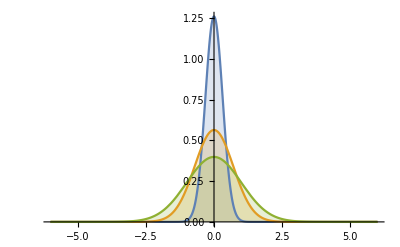

```mathematica
Plot[Table[PDF[NormalDistribution[0,1/√(2γ)],x],{γ,{5,1,.5}}]//Evaluate,{x,-6,6},Filling->Axis,PlotRange->Full]
```

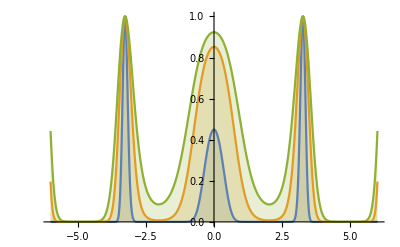

```mathematica
Plot[Table[Exp[-γ (x Sin[x]+.4)^2],{γ,{5,1,.5}}]//Evaluate,{x,-6,6},Filling->Axis]
```

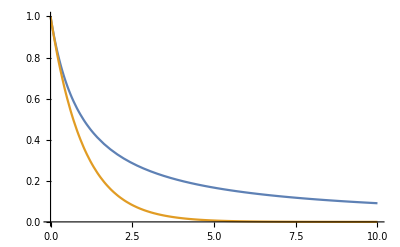

```mathematica
Plot[{1/(d+1),Exp[-d]},{d,0,10},PlotRange->Full]
```